ⅇ^(-x-3 y) (-1+ⅇ^(3 y)) Sinh[x]

Plot3D::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

-Graphics3D-

Plot3D::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

-Graphics3D-

ContourPlot::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

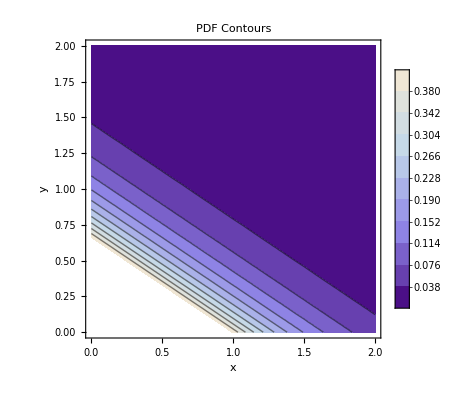

ContourPlot::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

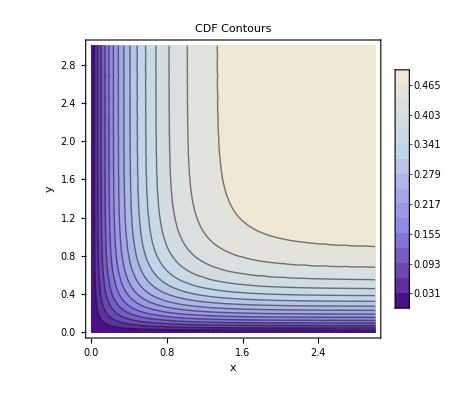

```mathematica
(*Define joint PDF*)f[x_,y_]:=3 Exp[-(2 x+3 y)]

(*Compute joint CDF analytically*)
F[x_,y_]=Integrate[f[u,v],{u,0,x},{v,0,y},Assumptions->{x>0,y>0}]//Simplify

(*Simplified closed form*)
F[x_,y_]=(1/2) (1-Exp[-2 x]) (1-Exp[-3 y]);

(*---3D surface plots---*)
pdfPlot=Plot3D[f[x,y],{x,0,3},{y,0,3},PlotRange->All,AxesLabel->{"x","y","f(x,y)"},PlotLabel->"Joint PDF f(x,y)",ColorFunction->"Viridis"]

cdfPlot=Plot3D[F[x,y],{x,0,3},{y,0,3},PlotRange->All,AxesLabel->{"x","y","F(x,y)"},PlotLabel->"Joint CDF F(x,y)",ColorFunction->"Viridis"]

(*---Contour plots---*)
pdfContour=ContourPlot[f[x,y],{x,0,2},{y,0,2},Contours->10,ColorFunction->"Viridis",PlotLegends->Automatic,FrameLabel->{"x","y"},PlotLabel->"PDF Contours"]

cdfContour=ContourPlot[F[x,y],{x,0,3},{y,0,3},Contours->15,ColorFunction->"Viridis",PlotLegends->Automatic,FrameLabel->{"x","y"},PlotLabel->"CDF Contours"]

(*Display plots together*)
GraphicsGrid[{{pdfPlot,cdfPlot},{pdfContour,cdfContour}}];
```

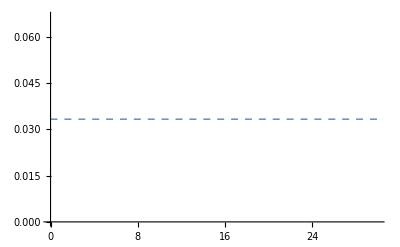

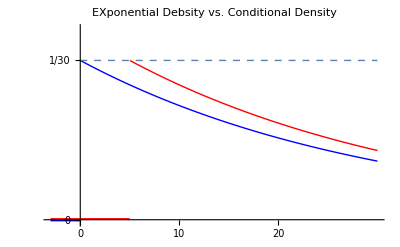

```mathematica
f[x_]:=Piecewise[{{Exp[-(x-5)/30]/30,5<x},{0.0002,-3<x≤5}}]
g[x_]:=Piecewise[{{Exp[-x/30]/30,0<=x},{-0.0002,x<0}}]
a=Plot[f[x],{x,-3,30},PlotRange->{-0.0005,1.2/30},PlotStyle->{Red,Thick},Ticks->{{0,5,10,15,20,25},{0,1/30}}];
b=Plot[g[x],{x,-3,30},PlotRange->{-0.0005,1.2/30},PlotStyle->{Blue,Thick},Ticks->{{0,5,10,15,20,25},{0,1/30}}];
c=Plot[1/30,{x,0,30},PlotStyle->{Dashed,Thick}]
Show[a,b,c,PlotLabel->"EXponential Debsity vs. Conditional Density"]
```

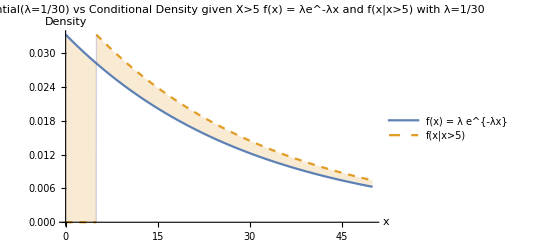

```mathematica
(*Parameter*)lambda=1/30;

(*Define the original exponential pdf*)
f[x_]:=Piecewise[{{lambda Exp[-lambda x],x≥0}},0];

(*Conditional pdf given X>5*)
fcond[x_]:=Piecewise[{{lambda Exp[-lambda (x-5)],x≥5}},0];

(*Plot both densities*)
Plot[{f[x],fcond[x]},{x,0,50},PlotRange->All,PlotStyle->{Thick,{Thick,Dashed}},PlotLegends->{"f(x) = λ e^{-λx}","f(x|x>5)"},AxesLabel->{"x","Density"},PlotLabel->"               Exponential(λ=1/30) vs Conditional Density given X>5\n f(x) = λe^-λx and f(x|x>5) with λ=1/30",Filling->{2->{1}}]
```

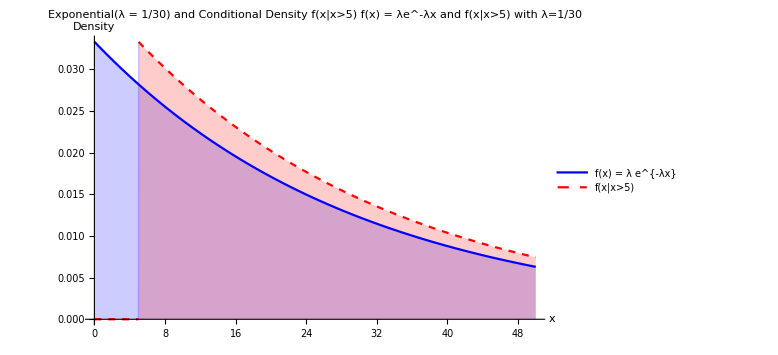

```mathematica
(*Parameter*)lambda=1/30;

(*Define the original exponential pdf*)
f[x_]:=Piecewise[{{lambda Exp[-lambda x],x≥0}},0];

(*Conditional pdf given X>5*)
fcond[x_]:=Piecewise[{{lambda Exp[-lambda (x-5)],x≥5}},0];

(*Plot both densities with colored shading*)
Plot[{f[x],fcond[x]},{x,0,50},PlotRange->All,PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},Filling->{1->{Axis,{Opacity[0.2,Blue]}},(*shade under original pdf*)2->{Axis,{Opacity[0.2,Red]}}     (*shade under conditional pdf*)},PlotLegends->{"f(x) = λ e^{-λx}","f(x|x>5)"},AxesLabel->{"x","Density"},PlotLabel->"Exponential(λ = 1/30) and Conditional Density f(x|x>5)\n f(x) = λe^-λx and f(x|x>5) with λ=1/30",ImageSize->Large]
```